## Appendix

We first generate the matrix X for N=100 points on a square bounded between 0 and 1 from a uniform distribution.

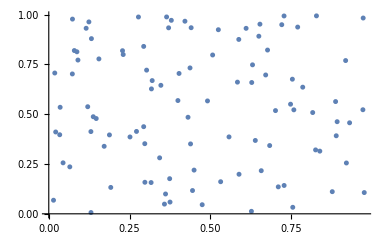

```mathematica
SeedRandom[1994];
X=RandomReal[{0,1},{100,2}];
ListPlot[X]
(*SeedRandom[] is a pre-generated set of pseudorandom numbers. 1994 was arbitrary *)
```

The matrix W is given by the pairwise distances between each point in X.

```mathematica
W=DistanceMatrix[X,DistanceFunction->SquaredEuclideanDistance];
```

```mathematica
(∑_(j=1)^100 ∑_(i=1)^100 W⟦i,j⟧-∑_(i=1)^100 W⟦i,i⟧)/(100*100-100)
```

0.339345

We generate A_i randomly from a Pareto distribution with minimum value parameter k=1 and shape parameter α=1. First we take a random draw from the distribution to get A1.

```mathematica
SeedRandom[104];
A1=RandomVariate[ParetoDistribution[1,1],{100,1}];
```

Then we normalize each entry by subtracting the mean and dividing by the standard deviation to allow negative values to get our A vector.

```mathematica
A=(A1-Mean[A1]⟦1⟧ConstantArray[1,{100,1}])/(StandardDeviation[A1]⟦1⟧);
```

Next, we will generate the matrix U from a logistic distribution with mean 0 and scale parameter 1 to compare with the link surplus created by the above terms in the model. We computer a different value of U for each time step U[0], U[1], U[2], corresponding to t=0,t=1,t=2, respectively.

```mathematica
SeedRandom[105];
U[0]=SymmetrizedArray[{{i_,j_}:>RandomVariate[LogisticDistribution[Mean[A1]⟦1⟧,1]]/;0<Abs[i-j]≤100},{100,100},Symmetric[{1,2}]];
```

```mathematica
SeedRandom[106];
U[1]=SymmetrizedArray[{{i_,j_}:>RandomVariate[LogisticDistribution[Mean[A1]⟦1⟧,1]]/;0<Abs[i-j]≤100},{100,100},Symmetric[{1,2}]];
```

```mathematica
SeedRandom[107];
U[2]=SymmetrizedArray[{{i_,j_}:>RandomVariate[LogisticDistribution[Mean[A1]⟦1⟧,1]]/;0<Abs[i-j]≤100},{100,100},Symmetric[{1,2}]];
```

Now with the given draw of U_ij and a given value of β, we can derive the adjacency matrix for the network. For example, if β=-1070, we use the rule:

D_ij=1(W_ij β+A_i+A_j-U_ij≥0),

to get the following adjacency matrix.

```mathematica
β=-0.0002;
```

```mathematica
d[0]=Table[Boole[(β W⟦i,j⟧+A⟦i⟧+A⟦j⟧-U[0]⟦i,j⟧)⟦1⟧≥0&&i≠j],{i,1,100},{j,1,100}];
```

Initial network for t=0. Size of vertex increases with vertex degree.

```mathematica
graph1=AdjacencyGraph[d[0],VertexCoordinates->X,Axes->True,AxesOrigin->{0,0},PlotLabel->"t = 0"];
vd1=Thread[VertexList@graph1->30*Normalize[VertexDegree@graph1,Total]];
Show[SetProperty[graph1,VertexSize->vd1],ListPlot[X]]
```

-Graphics-

R(t) measures the number of links agents i and j have in common.

```mathematica
R[t_]:=Table[∑_(k=1)^100 d[t]⟦i,k⟧d[t]⟦k,j⟧,{i,1,100},{j,1,100}]
```

```mathematica
R0=R[0];
```

```mathematica
R[1]=Table[∑_(k=1)^100 d[1]⟦i,k⟧d[1]⟦k,j⟧,{i,1,100},{j,1,100}];
```

```mathematica
α=0.1;
γ=-0.0002;
```

```mathematica
d[t_]:=d[0]
```

```mathematica
d[t_]:=Piecewise[{{Table[Boole[(α d[t-1]⟦i,j⟧+γ R[t-1]⟦i,j⟧+A⟦i⟧+A⟦j⟧-U[t]⟦i,j⟧)⟦1⟧≥0&&i≠j],{i,1,100},{j,1,100}], t>0}, {d[0], t==0}}]
```

Network graph for t=1. Size of vertex increases with vertex degree.

```mathematica
d[1]=Table[Boole[(α d[0]⟦i,j⟧+γ R0⟦i,j⟧+A⟦i⟧+A⟦j⟧-U[1]⟦i,j⟧)⟦1⟧≥0&&i≠j],{i,1,100},{j,1,100}];
```

```mathematica
graph2=AdjacencyGraph[d[1],VertexCoordinates->X,Axes->True,AxesOrigin->{0,0},PlotLabel->"t = 1"];
vd2=Thread[VertexList@graph2->40*Normalize[VertexDegree@graph2,Total]];
Show[SetProperty[graph2,VertexSize->vd2],ListPlot[X]]
```

-Graphics-

```mathematica
d[2]=Table[Boole[(α d[1]⟦i,j⟧+γ R[1]⟦i,j⟧+A⟦i⟧+A⟦j⟧-U[2]⟦i,j⟧)⟦1⟧≥0&&i≠j],{i,1,100},{j,1,100}];
```

```mathematica
graph3=AdjacencyGraph[d[2],VertexCoordinates->X,Axes->True,AxesOrigin->{0,0},PlotLabel->"t = 2"];
vd3=Thread[VertexList@graph3->40*Normalize[VertexDegree@graph3,Total]];
Show[SetProperty[graph3,VertexSize->vd3],ListPlot[X]]
```

-Graphics-